## Author: Sreenath K. Manikandan, Nordita, KTH Royal Institute of Technology and Stockholm University

## Single qubit clock example

```mathematica
omega=.;k=.;gamma=.;dt=.;
```

```mathematica
H0=omega{{1,0},{0,0}};
```

```mathematica
sx={{0,1},{1,0}};k=.;rho={{r11,r12},{r21,r22}};rhs={{r11,rx-I ry},{rx+I ry,1-r11}};Ad={{0,1},{0,0}};Aa={{0,0},{1,0}};
dt(-I (H0.rho-rho.H0)+k Exp[-s]Aa.rho.Ad-k/2(Ad.Aa.rho+rho.Ad.Aa))-gamma (sx.(sx.rho-rho.sx)-(sx.rho-rho.sx).sx)dt
```

{{-dt k r11-dt gamma (2 r11-2 r22),dt (-(k r12)/2-ⅈ omega r12)-dt gamma (2 r12-2 r21)},{-dt gamma (-2 r12+2 r21)+dt (-(k r21)/2+ⅈ omega r21),dt ⅇ^-s k r11-dt gamma (-2 r11+2 r22)}}

The above is the tilted Lindblad generator

## Solution for steady state (when s=0):

```mathematica
Solve[dt(-I (H0.rhs-rhs.H0)+k Aa.rhs.Ad-k/2(Ad.Aa.rhs+rhs.Ad.Aa))-gamma (sx.(sx.rhs-rhs.sx)-(sx.rhs-rhs.sx).sx)dt=={{0,0},{0,0}},{r11,rx,ry}]
```

{{r11→(2 gamma)/(4 gamma+k),rx→0,ry→0}}

```mathematica
rst={{r11->(2 gamma)/(4 gamma+k),rx->0,ry->0}};
```

## We now proceed to compute the eigenvalues of the tilted Lindblad generator

```mathematica
Eqs={-dt k r11-dt gamma (2 r11-2 r22),dt (-(k r12)/2-ⅈ omega r12)-dt gamma (2 r12-2 r21),-dt gamma (-2 r12+2 r21)+dt (-(k r21)/2+ⅈ omega r21),dt ⅇ^-s k r11-dt gamma (-2 r11+2 r22)}
```

{-dt k r11-dt gamma (2 r11-2 r22),dt (-(k r12)/2-ⅈ omega r12)-dt gamma (2 r12-2 r21),-dt gamma (-2 r12+2 r21)+dt (-(k r21)/2+ⅈ omega r21),dt ⅇ^-s k r11-dt gamma (-2 r11+2 r22)}

```mathematica
ldss=Normal@CoefficientArrays[Eqs,{r11,r12,r21,r22}][[2]]/dt//Simplify
```

{{-2 gamma-k,0,0,2 gamma},{0,-2 gamma-k/2-ⅈ omega,2 gamma,0},{0,2 gamma,-2 gamma-k/2+ⅈ omega,0},{2 gamma+ⅇ^-s k,0,0,-2 gamma}}

```mathematica
Eigenvalues[ldss]//FullSimplify
```

{-1/2 ⅇ^-s (ⅇ^s (4 gamma+k)+√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2)))),1/2 ⅇ^-s (-ⅇ^s (4 gamma+k)+√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2)))),-2 gamma-k/2-ⅇ^-s √(ⅇ^(2 s) (4 gamma^2-omega^2)),-2 gamma-k/2+ⅇ^-s √(ⅇ^(2 s) (4 gamma^2-omega^2))}

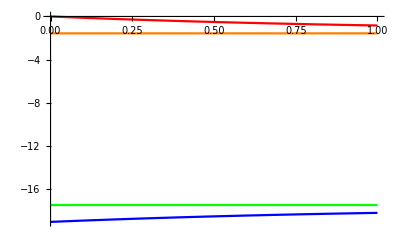

```mathematica
k=3;gamma=4;omega=1;Plot[{-1/2 ⅇ^-s (ⅇ^s (4 gamma+k)+√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2)))),1/2 ⅇ^-s (-ⅇ^s (4 gamma+k)+√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2)))),-2 gamma-k/2-ⅇ^-s √(ⅇ^(2 s) (4 gamma^2-omega^2)),-2 gamma-k/2+ⅇ^-s √(ⅇ^(2 s) (4 gamma^2-omega^2))},{s,0,1},PlotStyle->{Blue,Red,Green,Orange}]
```

## Large deviation form as the largest real eigenvalue

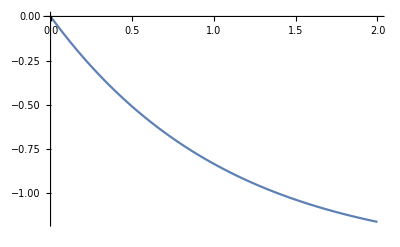

```mathematica
k=3;Plot[1/2 ⅇ^-s (-ⅇ^s (4 gamma+k)+√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2)))),{s,0,2}]
```

```mathematica
rho=.;k=.;
```

```mathematica
gamma=.;
k=6;
omega=1;dt=0.001;H0=omega{{1,0},{0,0}};sx={{0,1},{1,0}};t4=Table[{gamma,ct={};ct1={};ct2={};Do[For[n=0,n<1000+1,n++,rho[0]={{(2 gamma)/(4 gamma+k),0},{0,1-(2 gamma)/(4 gamma+k)}};M0={{Sqrt[1-k dt],0},{0,1}};M1={{0,0},{Sqrt[k dt],0}};M[n]=RandomChoice[{Chop[Tr[M0.(rho[n]-dt I (H0.rho[n]-rho[n].H0)-gamma (sx.(sx.rho[n]-rho[n].sx)-(sx.rho[n]-rho[n].sx).sx)dt).Transpose[M0]]],1-Chop[Tr[M0.(rho[n]-dt I (H0.rho[n]-rho[n].H0)-gamma (sx.(sx.rho[n]-rho[n].sx)-(sx.rho[n]-rho[n].sx).sx)dt).Transpose[M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=M[n].(rho[n]-dt I (H0.rho[n]-rho[n].H0)-gamma (sx.(sx.rho[n]-rho[n].sx)-(sx.rho[n]-rho[n].sx).sx)dt).Transpose[M[n]]/Tr[M[n].(rho[n]-dt I (H0.rho[n]-rho[n].H0)-gamma (sx.(sx.rho[n]-rho[n].sx)-(sx.rho[n]-rho[n].sx).sx)dt).Transpose[M[n]]];
];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];AppendTo[ct2,Total[Table[count[n],{n,0,1000}]]];,{5000}];Mean[ct],Mean[ct1],Mean[ct2],Variance[ct2]},{gamma,0.1,10.1,1}]
```

```mathematica
t4={{0.1,0.00018741258741269778,0.00018739260739260747,0.18760000000011207,0.17244072814562905},{1.1,0.001273526473526582,0.0012721926073926077,1.2748000000001132,0.9850819763952786},{2.1,0.0017842157842158923,0.001781450549450549,1.7860000000001135,1.3644768953790751},{3.1,0.0020629370629371706,0.002059118081918081,2.0650000000001136,1.6238997799559902},{4.1,0.002248951048951157,0.002244340059940058,2.2512000000001136,1.7992584116823354},{5.1,0.00231308691308702,0.0023081326673326658,2.3154000000001136,1.9139056211242238},{6.1,0.002448951048951156,0.0024432487512487493,2.4514000000001137,2.1504681336267244},{7.1,0.0024787212787213855,0.002472896703296702,2.4812000000001135,2.155677695539107},{8.1,0.0025158841158842227,0.0025098537462537453,2.5184000000001134,2.21290402080416},{9.1,0.0026031968031969095,0.002596710089910089,2.6058000000001136,2.3092682136427274},{10.1,0.0026447552447553513,0.0026380811188811176,2.6474000000001134,2.319937227445488}};
```

```mathematica
⟨N⟩
```

⟨N⟩

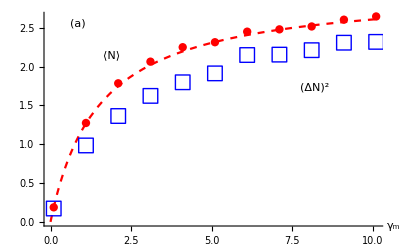

```mathematica
dt=0.001;k=6;pwa=Show[Plot[(2 gamma)/(4 gamma+k)k 1000dt,{gamma,0,10.1},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black]},PlotRange->All,Epilog->{{Style[Text["⟨N⟩",Scaled[{0.2,0.8}]],16,Red]},{Style[Text["(a)",Scaled[{0.1,0.95}]],16,Black]},{Style[Text["(ΔN)^2",Scaled[{0.8,0.65}]],16,Blue]}}],ListPlot[Table[{t4[[i]][[1]],t4[[i]][[4]]},{i,1,Length[t4]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{t4[[i]][[1]],t4[[i]][[5]]},{i,1,Length[t4]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

```mathematica
gamma=.;k=.;-D[1/2 ⅇ^-s (-ⅇ^s (4 gamma+k)+√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2)))),s]//FullSimplify
```

(2 gamma k)/(√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2))))

```mathematica
ff[s_]:=(2 gamma k)/(√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2))))
```

```mathematica
ff[0]//FullSimplify
```

(2 gamma k)/(√((4 gamma+k)^2))

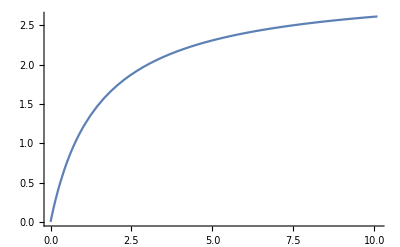

```mathematica
k=6;p1=Plot[(2 gamma k)/(√((4 gamma+k)^2))1000dt,{gamma,0,10.1},PlotRange->All]
```

```mathematica
D[1/2 ⅇ^-s (-ⅇ^s (4 gamma+k)+√(ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2)))),{s,2}]//FullSimplify
```

```mathematica
fg[s_]:=(2 ⅇ^s gamma k (4 gamma k+ⅇ^s (16 gamma^2+k^2)))/((ⅇ^s (8 gamma k+ⅇ^s (16 gamma^2+k^2)))^(3/2))
```

```mathematica
fg[0]//FullSimplify
```

(2 gamma k (16 gamma^2+4 gamma k+k^2))/(((4 gamma+k)^2)^(3/2))

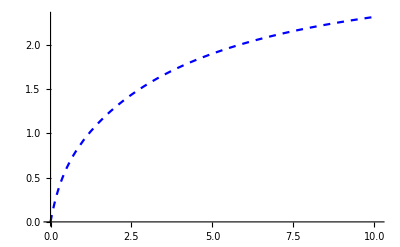

```mathematica
k=6;p2=Plot[(2 gamma k (16 gamma^2+4 gamma k+k^2))/(((4 gamma+k)^2)^(3/2))1000dt,{gamma,0,10.1},PlotStyle->{Dashed,Blue}]
```

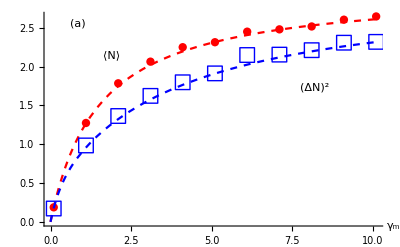

```mathematica
plot1=Show[pwa,p2]
```

```mathematica
k=6;q1=Plot[{-0.25,(2 gamma k (16 gamma^2+4 gamma k+k^2))/(((4 gamma+k)^2)^(3/2))/((2 gamma k)/(√((4 gamma+k)^2))) -1},{gamma,0,10.1},PlotRange->{All,{0,-0.4}},PlotStyle->{{Dashed,Blue},{Dashed,Red}},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black],Style["Q",Italic,24,Black]},PlotRange->All,Epilog->{{Style[Text["(b)",Scaled[{0.1,0.9}]],16,Black]},{Style[Text["Q=-0.25",Scaled[{0.8,0.3}]],16,Blue]}}];
```

```mathematica
q2=ListPlot[Table[{t4[[i]][[1]],t4[[i]][[5]]/t4[[i]][[4]]-1},{i,1,Length[t4]}], PlotMarkers->{"□",15},PlotStyle->{Red}];
```

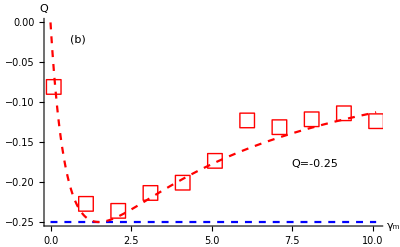

```mathematica
plot2=Show[q1,q2]
```

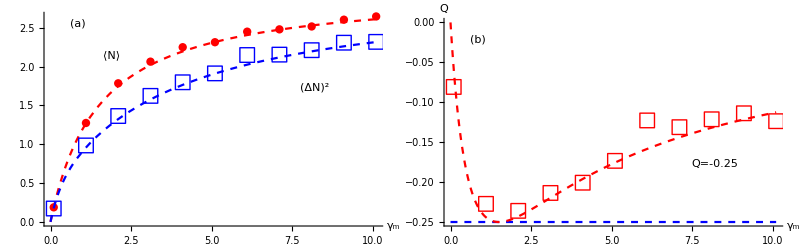

```mathematica
GraphicsGrid[{{plot1,plot2}},Spacings->{0, 0},ImageSize->800]
```

```mathematica
(2 gamma kk (16 gamma^2+4 gamma kk+kk^2))/(((4 gamma+kk)^2)^(3/2))/((2 gamma kk)/(√((4 gamma+kk)^2))) -1//FullSimplify
```

-(4 gamma kk)/(4 gamma+kk)^2